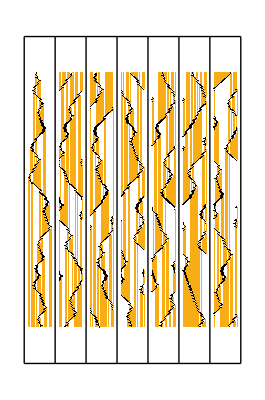

```mathematica
With[{rule={{1,0}->{3,1,-1},{1,1}->{3,0,1},{2,0}->{4,1,-1},{2,1}->{2,0,1},{3,0}->{2,1,1},{3,1}->{4,1,-1},{4,0}->{1,1,1},{4,1}->{4,0,-1}}},GraphicsRow[RulePlot[TuringMachine[rule],#,]&/@NestList[TuringMachine[rule,#[[-1]],250]&,{{1,{{},0}}},7][[2;;]],]]
```